1. Дана конечная струна длины L = 1, закрепленная на концах . Начальное смещение ноль и f (x, t) = 0. Начальная скорость представлена на рисунке . Построить профиль струны .

-Graphics-

```mathematica
stc[x_,w_] =( w/(2*Pi))* ArcCos[Cos[2*Pi*x/w]]
```

(w ArcCos[Cos[(2 π x)/w]])/(2 π)

Пусть начальная скорость 0, кроме двух отрезков: [0.2;0.3] - скорость равна 1 и [0.7;0.8] - скорость равна -1

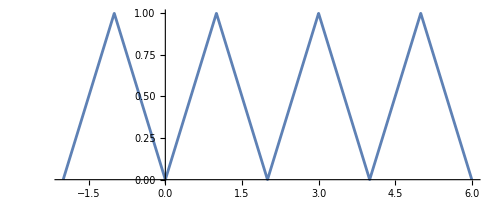

```mathematica
Plot[stc[x,2],{x,-2,6},AspectRatio->Automatic]
```

Зададим кусочную функцию начальной скорости:

```mathematica
ψ[x_] = Piecewise[{{0,x<=0.2},{1,x<=0.3},{0,x<=0.7},{-1,x<=0.8}},0]
```

Piecewise[{{0, x≤0.2}, {1, x≤0.3}, {0, x≤0.7}, {-1, x≤0.8}, {0, True}}]

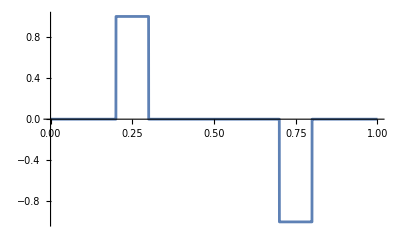

```mathematica
Plot[ψ[x],{x,0,1}, Exclusions->None]
```

```mathematica
a=.;v1[x_,t_]=1/(2*a)*Simplify[Integrate[ψ[τ],{τ,α,β},Assumptions:>α>0&&β>0]]
u1[x_,t_]=v1[x,t]/. {α->stc[x-a*t,2*L],β->stc[x+a*t,2*L]};
a=1;L=1;T=Range[0,1.98,0.02]
Animate[Plot[u1[x,t],{x,0,1},PlotRange->{-0.12,0.12},PlotLabel->t],{t,T},AnimationRunning->False]
```

((Piecewise[{{-0.1, (0.<α≤0.7&&β>0.8)||(α>0.3&&0.<β≤0.2)}, {0.2-1. α, 0.2<α≤0.3&&0.<β≤0.2}, {-0.8+α, 0.7<α≤0.8&&β>0.8}, {0.7-1. β, 0.<α≤0.7&&0.7<β≤0.8}, {α-1. β, 0.7<α≤0.8&&α<β&&β≤0.8}, {-0.3+β, 0.2<β<0.3&&α>0.3}, {-1. α+β, 0.2<α≤0.3&&β>0.2&&α>β}, {0., True}}])+(Piecewise[{{0.1, (α>0.8&&0.<β≤0.7)||(0.<α≤0.2&&β>0.3)}, {0.8-1. β, α>0.8&&0.7<β<0.8}, {-0.2+β, 0.<α≤0.2&&0.2<β≤0.3}, {0.3-1. α, 0.2<α<0.3&&β>0.3}, {-1. α+β, 0.2<α<0.3&&α<β≤0.3}, {-0.7+α, 0.7<α≤0.8&&0.<β≤0.7}, {α-1. β, 0.7<α≤0.8&&0.7<β<α}, {0., True}}]))/(2 a)

{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98}

2. Дана конечная струна длины L = 1, закрепленная на концах . В начальный момент начальная скорость равна нулю и f (x, t) = 0, а начальное отклонение представлено на рисунке. Построить профиль струны.

```mathematica
ψ2[x_] = Piecewise[{{0,x<=0.2},{5*x -1,x<=0.4},{-5*x +3,x<=0.8}},0 ]
```

Piecewise[{{0, x≤0.2}, {-1+5 x, x≤0.4}, {3-5 x, x≤0.8}, {0, True}}]

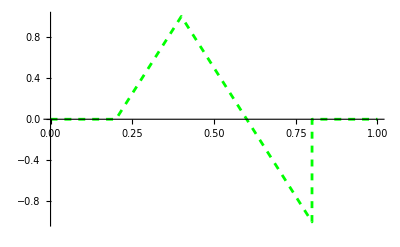

```mathematica
Plot[ψ2[x],{x,0,1}, Exclusions->None,  PlotStyle->{Green, Dashed}]
```

```mathematica
a =.;u2[x_,t_]=(1/2)*(Power[-1,Floor[(x+at)/L]]*ψ2[stc[x+at,2*L]]+ Power[-1,Floor[(x-at)/L]] * ψ2[stc[x-at,2*L]])
```

1/2 ((-1)^Floor[-at+x] (Piecewise[{{0, ArcCos[Cos[π (-at+x)]]/π≤0.2}, {-1+(5 ArcCos[Cos[π (-at+x)]])/π, ArcCos[Cos[π (-at+x)]]/π≤0.4}, {3-(5 ArcCos[Cos[π (-at+x)]])/π, ArcCos[Cos[π (-at+x)]]/π≤0.8}, {0, True}}])+(-1)^Floor[at+x] (Piecewise[{{0, ArcCos[Cos[π (at+x)]]/π≤0.2}, {-1+(5 ArcCos[Cos[π (at+x)]])/π, ArcCos[Cos[π (at+x)]]/π≤0.4}, {3-(5 ArcCos[Cos[π (at+x)]])/π, ArcCos[Cos[π (at+x)]]/π≤0.8}, {0, True}}]))

```mathematica
a=1;L=1;T=Range[0,1.98,0.02];
```

```mathematica
Animate[Plot[u2[x,t],{x,0,1},PlotRange->{-1,1},PlotLabel->t],{t,0,2,0.02},AnimationRunning->False]
```